Here we will look at Hutchinson’s solution to his paradox of the plankton: “the diversity of the phytoplankton was explicable primarily by a permanent failure to achieve equilibrium as the relevant external factors changed.”  We will consider two types of these fluctuation-dependent coexistence mechanisms (Chesson 2000): relative nonlinearity and the storage effect.

```mathematica
<<EcoEvo`
```

EcoEvo Package Version 1.7.2 (September 1, 2023)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

## Relative nonlinearity

This coexistence mechanism has two key ingredients: fluctuating resource levels (here driven as alternating good & bad seasons) and crossing growth curves (a gleaner-opportunist trade-off).

During the good season (ϕ proportion of the period), species compete for one resource R according to

(d n_1)/dt=(f_1(R)-m)n_1
(d n_2)/dt=(f_2(R)-m)n_2

During the bad season (1-ϕ proportion of the period), species just die off exponentially:

(d n_1)/dt=-m_1 n_1
(d n_2)/dt=-m_2 n_2

In both cases, we model the available resource as an algebraic expression (instead of a chemostat), where R_tot is the total amount of resource in a closed system (similar to R_in in a chemostat model):

R=R_tot-n_1-n_2

```mathematica
SetModel[{
Pop[n1]->{Equation:>n1(e*f1[R]-m),Color->Green},
Pop[n2]->{Equation:>n2(e*f2[R]-m),Color->Darker@Green},
Period:>τ
}];
R:=Rtot-n1-n2;

(* functional response *)
f1[R_]:=μ1 R/(R+h1);
f2[R_]:=μ2 R/(R+h2);

(* growing season switch - e=1 in good season, e=0 in bad season *)
e:=If[Mod[t,τ]<ϕ τ,1,0];
```

Plot the environmental forcing function.

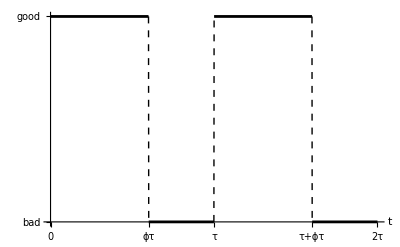

```mathematica
τ=1; (* period *)
ϕ=0.6; (* good season fraction of period, 0 <= ϕ <= 1 *)

Plot[e,{t,0,2τ},AxesLabel->{"t"},PlotStyle->Black,ExclusionsStyle->Dashed,Ticks->{{{0,0},{ϕ τ,"ϕτ"},{τ,"τ"},{(1+ϕ) τ,"τ+ϕτ"},{2τ,"2τ"}},{{0,"bad"},{1,"good"}}},PlotRangePadding->0.01]
```

Plot growth curves.  Is there a gleaner-opportunist trade-off?

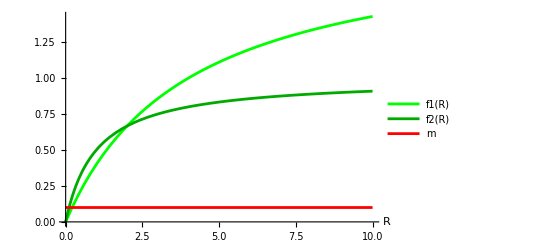

```mathematica
μ1=2;μ2=1; (* max growth rate *)
h1=4;h2=1; (* half-saturation constant *)
m=0.1; (* mortality rate *)

(* plot growth vs R and mortality *)
Plot[{f1[R],f2[R],m},{R,0,10},PlotStyle->{Color[n1],Color[n2],Red},AxesLabel->{"R"},PlotLegends->{"f1(R)","f2(R)","m"}]
```

Yes, the curves cross so n2 is a better competitor (a gleaner) but n1 is better at high resource levels (an opportunist).

Run some simulations where you vary the good fraction of the period, ϕ.  How does the outcome change?

```mathematica
Rtot=10; (* resource supply *)
τ=10; (* period (0 < τ ≤ 300) *)
```

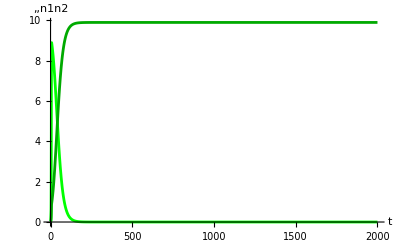

```mathematica
ϕ=1.0; (* good season fraction of period, 0 <= ϕ <= 1 *)
sol=EcoSim[{n1->0.01,n2->0.01},200τ];
PlotDynamics[sol,{n1,n2},PlotPoints->400]
```

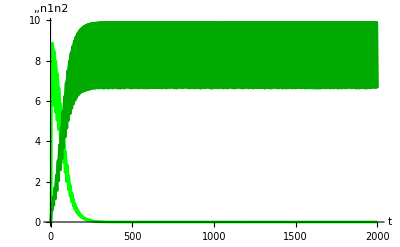

```mathematica
ϕ=0.6; (* growing fraction of period (0 ≤ ϕ ≤ 1) *)
sol=EcoSim[{n1->0.01,n2->0.01},200τ];
PlotDynamics[sol,{n1,n2},PlotPoints->400]
```

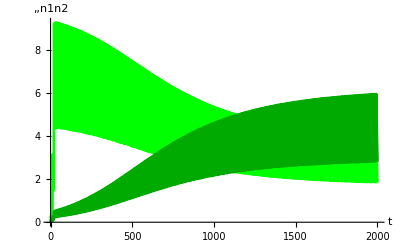

```mathematica
ϕ=0.25; (* growing fraction of period (0 ≤ ϕ ≤ 1) *)
sol=EcoSim[{n1->0.01,n2->0.01},200τ];
PlotDynamics[sol,{n1,n2},PlotPoints->400]
```

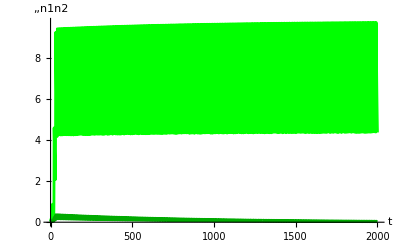

```mathematica
ϕ=0.2; (* growing fraction of period (0 ≤ ϕ ≤ 1) *)
sol=EcoSim[{n1->0.01,n2->0.01},200τ];
PlotDynamics[sol,{n1,n2},PlotPoints->400]
```

Dark green sp 2 (gleaner) wins for large ϕ, green sp 1 (opportunist) wins for small , they seem to coexist in between.

Now vary the period, τ  (you might need to increase tmax in EcoSim from 40τ).  How do the dynamics and the outcome change?

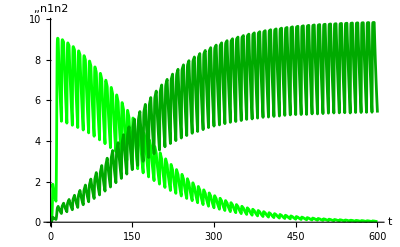

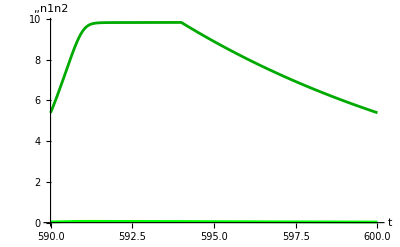

```mathematica
τ=10; (* period (0 < τ ≤ 300) *)
ϕ=0.4; (* growing fraction of period (0 ≤ ϕ ≤ 1) *)
sol=EcoSim[{n1->0.01,n2->0.01},60τ];
PlotDynamics[sol,{n1,n2},PlotPoints->200]

(* plot last period *)
PlotDynamics[FinalSlice[sol,τ],{n1,n2}]
```

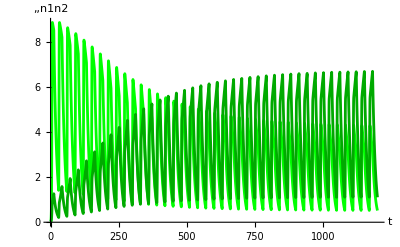

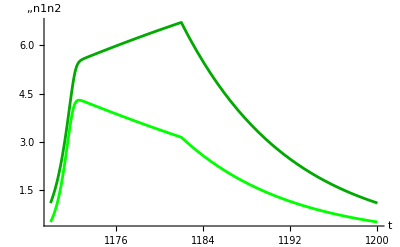

```mathematica
τ=30; (* period (0 < τ ≤ 300) *)
sol=EcoSim[{n1->0.01,n2->0.01},40τ];
PlotDynamics[sol,{n1,n2},PlotPoints->200]

(* plot last period *)
PlotDynamics[FinalSlice[sol,τ],{n1,n2}]
```

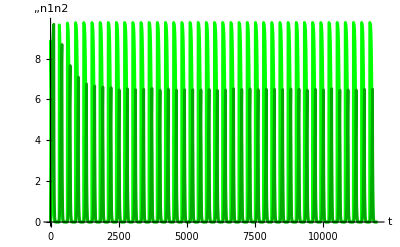

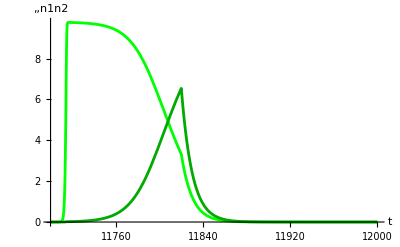

```mathematica
τ=300; (* period (0 < τ ≤ 300) *)
sol=EcoSim[{n1->0.01,n2->0.01},40τ];
PlotDynamics[sol,{n1,n2},PlotPoints->200]

(* plot last period *)
PlotDynamics[FinalSlice[sol,τ],{n1,n2}]
```

Population fluctuations become larger for larger period τ.  Coexistence seems easier for large τ.

Illustrate invasion criteria by solving for resident limit cycle, then plotting instantaneous invader growth rate over the period:

Infinity::indet: Indeterminate expression -∞+∞ encountered.

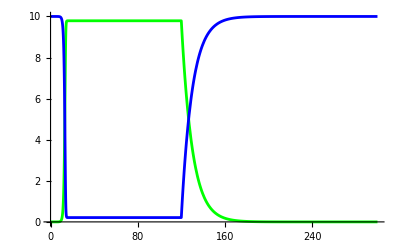

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

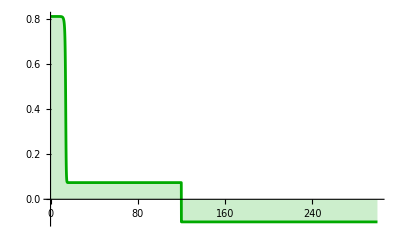

```mathematica
τ=300;
ec1=FindEcoCycle[FilterRules[FinalSlice[EcoSim[{n1->0.01},40τ]],n1]];
Plot[Evaluate[{n1[t],Rtot-n1[t]}/.ec1],{t,0,τ},PlotStyle->{Color[n1],Blue}]
Plot[Inv[ec1,n2,Method->"Instantaneous"],{t,0,τ},PlotStyle->Color[n2],PlotRange->All,Filling->Axis]
```

Inv integrates the instantaneous growth rate over one period:

```mathematica
Inv[ec1,n2]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {120.113}. NIntegrate obtained 1.01291 and 0.00815161 for the integral and error estimates.

0.00337637

Inv[ec1, n2]>0 means n2 can invade the n1 cycle. Now let's reverse the role of resident and invader:

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 120. and t = 120..

Infinity::indet: Indeterminate expression -∞+∞ encountered.

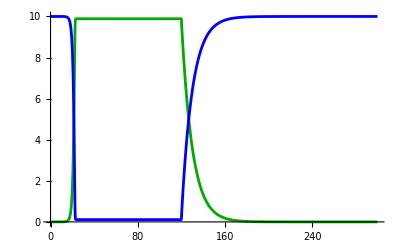

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

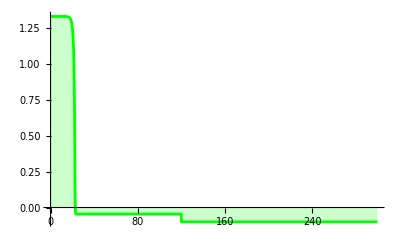

```mathematica
τ=300;
ec2=FindEcoCycle[FilterRules[FinalSlice[EcoSim[{n2->0.01},40τ]],n2]];
Plot[Evaluate[{n2[t],Rtot-n2[t]}/.ec2],{t,0,τ},PlotStyle->{Color[n2],Blue}]
Plot[Inv[ec2,n1,Method->"Instantaneous"],{t,0,τ},PlotStyle->Color[n1],PlotRange->All,Filling->Axis]
```

```mathematica
Inv[ec2,n1]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {120.113}. NIntegrate obtained 6.40885 and 0.00204824 for the integral and error estimates.

0.0213628

Inv[ec2, n1]>0 also, so therefore the two species satisfy the mutual invasion criterion for stable coexistence.

## Storage effect

Now instead alternating good and bad seasons, we will assume that growth depends unimodally on some external factor such as temperature.  If species differ in their optimal temperatures, then the outcome of competition in a constant environment would depend on temperature.  If the environment fluctuates so that each species has a time when they're the best competitor, might they coexist as Hutchinson (1961) suggested?

For simplicity, we assume linear functional responses f_i=μ_i R and a closed system as above:

(d n_1)/dt=(μ_1 R-m_1)n_1
(d n_2)/dt=(μ_2 R-m_2)n_2
	R=R_tot-n_1-n_2

The environmental factor, T[t], which could represent temperature, could affect either the density-independent death rate m_i(T) or the resource-dependent birth rate μ_i(T). We will look at both in turn to see if Hutchinson was correct that environmental variation can sidestep the Competitive Exclusion Principle and allow more than one species to coexist on one limiting resource.

```mathematica
Clear[μ1,μ2,m1,m2];
SetModel[{
Pop[n1]->{Equation:>(μ1 R-m1)n1,Color->Blue},
Pop[n2]->{Equation:>(μ2 R-m2)n2,Color->DarkYellow},
Period:>τ
}];
R:=Rtot-n1-n2;
```

### Temporally varying death

Here we assume that the death rate m_i increases quadratically away from a species-specific optimum temperature T_(opt,i) as

m_i=m+(T_(opt,i)-T)^2/σ^2

where m is a baseline temperature-independent death rate and σ measures the width of the temperature response.

```mathematica
m1:=m+(Topt1-T)^2/σ^2;
m2:=m+(Topt2-T)^2/σ^2;
```

```mathematica
Rtot=10; (* total resource *)
σ=2; (* width of temperature response *)
μ1=1.0; (* resource-dependent growth rate, sp. 1 *)
μ2=1.0; (* resource-dependent growth rate,sp.2 *)
m=0.1; (* baseline temperature-independent death rate *)
Topt1=-0.2; (* optimal temperature, sp 1 *)
Topt2=0.4; (* optimal temperature, sp 2 *)
```

Plot the death rate functions vs temperature (T).

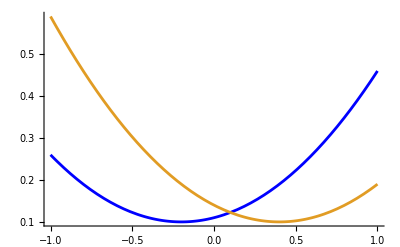

```mathematica
Plot[{m1,m2},{T,-1,1},PlotStyle->{Color[n1],Color[n2]},PlotRange->{0,All}]
```

Plot R* vs temperature for the two species.  For fixed T, what is the predicted outcome of competition?

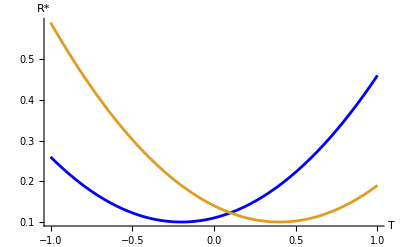

```mathematica
Plot[{m1/μ1,m2/μ2},{T,-1,1},PlotRange->{0,All},PlotStyle->{Color[n1],Color[n2]},AxesLabel->{"T","R*"}]
```

Looks like blue wins for T<0.1, yellow wins for T>0.1, neutral for T=0.1 (equal R*).

Verify your prediction using simulation by changing temperature T.

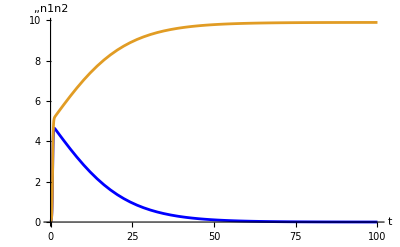

```mathematica
T=0.4; 
sol=EcoSim[{n1->0.01,n2->0.01},100];
PlotDynamics[sol,{n1,n2}]
```

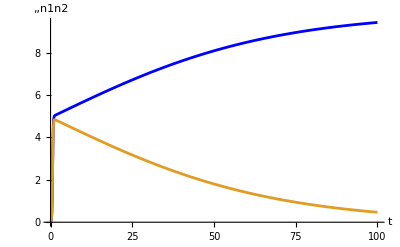

```mathematica
T=0; 
sol=EcoSim[{n1->0.01,n2->0.01},100];
PlotDynamics[sol,{n1,n2}]
```

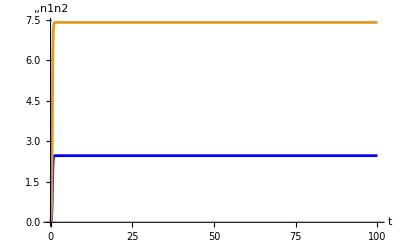

```mathematica
T=0.1; 
sol=EcoSim[{n1->0.01,n2->0.03},100];
PlotDynamics[sol,{n1,n2}]
```

Verified.

Now let T be a periodic function of time (sinusoidal).  There is a switch in the identity of the superior competitor each period.  Do you expect the two species to coexist?

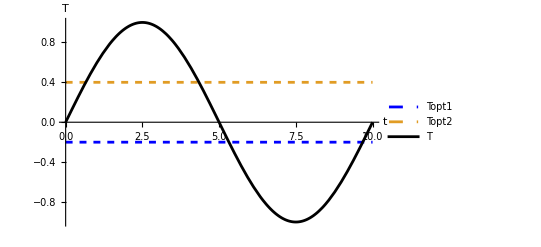

```mathematica
τ=10; (* period *)
T:=Sin[2π t/τ];
Plot[{Topt1,Topt2,T},{t,0,τ},AxesLabel->{"t","T"},PlotStyle->{{Dashed,Color[n1]},{Dashed,Color[n2]},Black},PlotLegends->{"Topt1","Topt2","T"}]
```

Seems plausible, because each species has a time when it's the best (lower R*).

Do they?

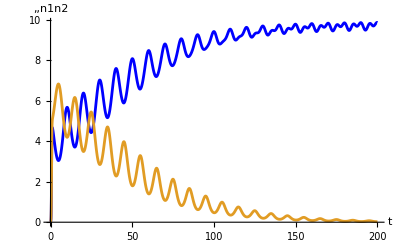

```mathematica
sol=EcoSim[{n1->0.01,n2->0.01,R->Rin},20τ];
PlotDynamics[sol,{n1,n2}]
```

No, yellow sp 2 is excluded?!

Can you find a way for the two species coexist by varying parameters?  If so, what did it take?  Is this coexistence robust?

We will vary the Topt of blue species 1:

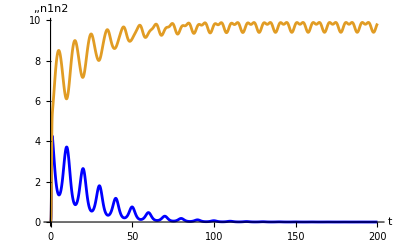

```mathematica
Topt1=-0.6; (* optimal temperature, sp 1 *)
Topt2=0.4; (* optimal temperature, sp 2 *)
sol=EcoSim[{n1->0.01,n2->0.01,R->Rin},20τ];
PlotDynamics[sol,{n1,n2}]
```

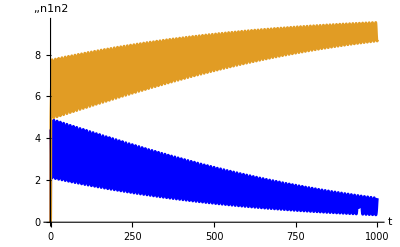

```mathematica
Topt1=-0.41; (* optimal temperature, sp 1 *)
Topt2=0.4; (* optimal temperature, sp 2 *)
sol=EcoSim[{n1->0.01,n2->0.01,R->Rin},100τ];
PlotDynamics[sol,{n1,n2}]
```

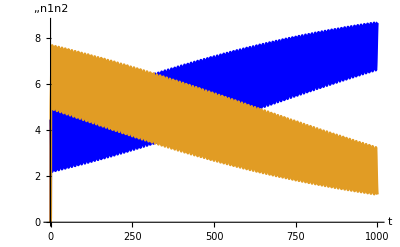

```mathematica
Topt1=-0.39; (* optimal temperature, sp 1 *)
Topt2=0.4; (* optimal temperature, sp 2 *)
sol=EcoSim[{n1->0.01,n2->0.01,R->Rin},100τ];
PlotDynamics[sol,{n1,n2}]
```

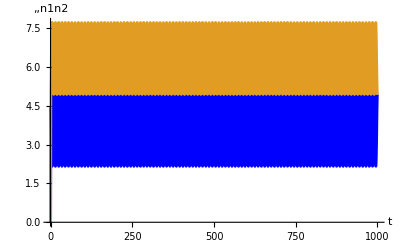

```mathematica
Topt1=-0.4; (* optimal temperature, sp 1 *)
Topt2=0.4; (* optimal temperature, sp 2 *)
sol=EcoSim[{n1->0.01,n2->0.01,R->Rin},100τ];
PlotDynamics[sol,{n1,n2}]
```

Looks like whichever species is best competitor on average excludes the other — no coexistence.

### Temporally varying birth

Now we will make the environmental variation affect the resource-dependent birth rate instead, by making the per-resource birth rate μ a Gaussian function of temperature.

```mathematica
Clear[m1,m2];
μ1:=μ E^(-(Topt1-T)^2/σ^2);
μ2:=μ E^(-(Topt2-T)^2/σ^2)
```

```mathematica
σ=0.6; (* width of temperature response *)
μ=1.0; (* per-resoruce resource-dependent growth rate *)
m1=0.1; (* temperature-independent mortality rate *)
m2=0.1; (*temperature-independent mortality rate*)
Topt1=-0.2; (* optimal temperature, sp 1 *)
Topt2=0.4; (* optimal temperature, sp 2 *)
```

Plot the per-resource birth rate functions vs temperature (T).

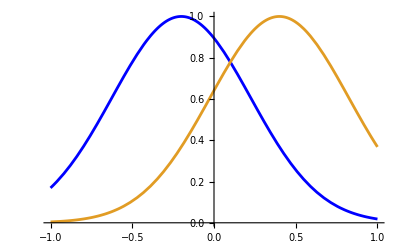

```mathematica
Plot[{μ1,μ2},{T,-1,1},PlotStyle->{Color[n1],Color[n2]},PlotRange->{0,All}]
```

Plot R* vs temperature (T) for the two species.

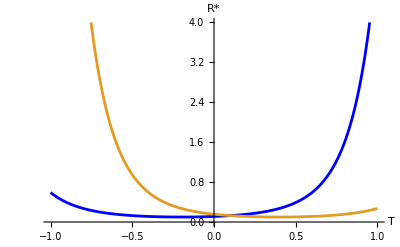

```mathematica
Plot[{m/μ1,m/μ2},{T,-1,1},PlotRange->{0,4},PlotStyle->{Color[n1],Color[n2]},AxesLabel->{"T","R*"}]
```

Again, looks like a switch in competitive ability at T=0.1.

Can you make the species coexist now?  Is this coexistence robust?

```mathematica
τ=10; (* period *)
```

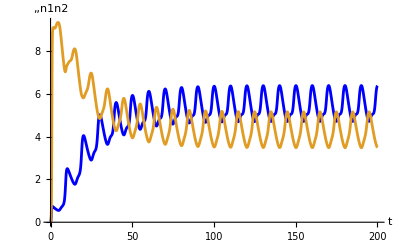

```mathematica
Topt1=-0.2; (* optimal temperature, sp 1 *)
Topt2=0.4; (* optimal temperature, sp 2 *)
sol=EcoSim[{n1->0.01,n2->0.01,R->Rin},20τ];
PlotDynamics[sol,{n1,n2}]
```

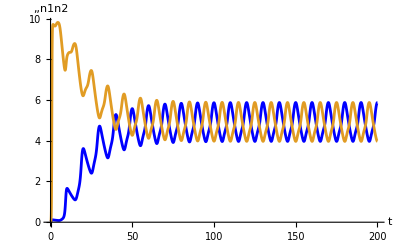

```mathematica
Topt1=-0.4; (* optimal temperature, sp 1 *)
Topt2=0.4; (* optimal temperature, sp 2 *)
sol=EcoSim[{n1->0.01,n2->0.01,R->Rin},20τ];
PlotDynamics[sol,{n1,n2}]
```

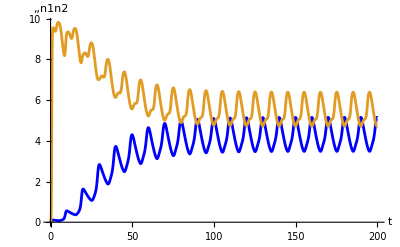

```mathematica
Topt1=-0.4; (* optimal temperature, sp 1 *)
Topt2=0.2; (* optimal temperature, sp 2 *)
sol=EcoSim[{n1->0.01,n2->0.01,R->Rin},20τ];
PlotDynamics[sol,{n1,n2}]
```

Looks like stable coexistence is fairly easy to attain in this case and doesn't require equal average competitive ability.

How do the dynamics and the outcome depend on the period τ ?

```mathematica
Topt1=-0.2; (* optimal temperature, sp 1 *)
Topt2=0.4; (* optimal temperature,sp 2 *)
```

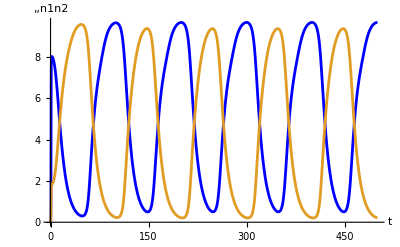

```mathematica
τ=100; (* period *)
sol=EcoSim[{n1->0.01,n2->0.01,R->Rin},5τ];
PlotDynamics[sol,{n1,n2}]
```

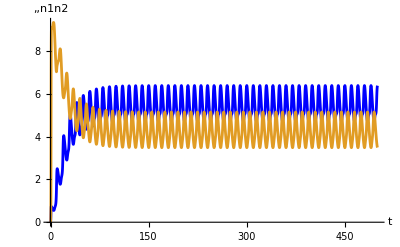

```mathematica
τ=10; (* period *)
sol=EcoSim[{n1->0.01,n2->0.01,R->Rin},50τ];
PlotDynamics[sol,{n1,n2}]
```

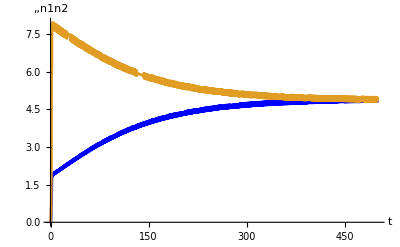

```mathematica
τ=1; (* period *)
sol=EcoSim[{n1->0.01,n2->0.01,R->Rin},500τ];
PlotDynamics[sol,{n1,n2}]
```

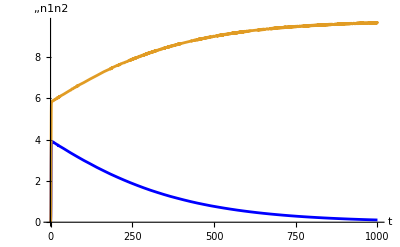

```mathematica
τ=0.1; (* period *)
sol=EcoSim[{n1->0.01,n2->0.01,R->Rin},10000τ];
PlotDynamics[sol,{n1,n2}]
```

Larger period τ makes higher amplitude population fluctuations.  Coexistence occurs except for very small period τ.

Speculate on what's the difference between the variable-death and variable-birth models that results in different potential for coexistence.

To be discussed in class.  See also Fox (2013).

### Decomposing invasion rates:

```mathematica
τ=100; (* period *)
sol=EcoSim[{n1->0.01,n2->0.01,R->Rin},5τ];
PlotDynamics[sol,{n1,n2}]
```

-Graphics-

Solve for n1 monoculture cycle:

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Infinity::indet: Indeterminate expression -∞+∞ encountered.

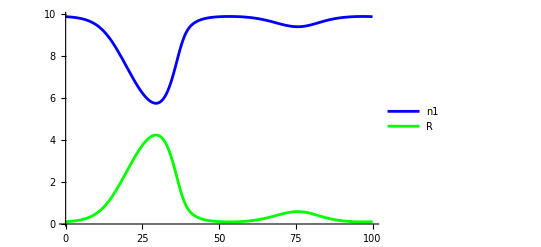

```mathematica
ec1=FindEcoCycle[FinalSlice[EcoSim[{n1->0.01,R->Rtot},5τ]]];
Plot[Evaluate[{n1[t],Rtot-n1[t]}/.ec1],{t,0,τ},PlotRange->{0,All},PlotStyle->{Color[n1],Green},PlotLegends->{"n1","R"}]
```

Plot μ1(T) and μ2(T) vs time.

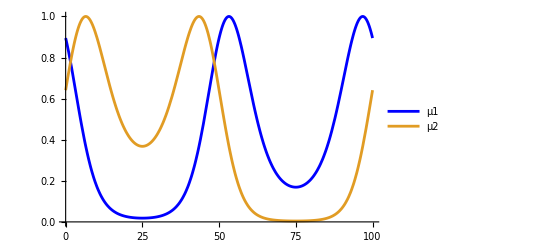

```mathematica
Plot[Evaluate[{μ1,μ2}/.ec1],{t,0,τ},PlotStyle->{Color[n1],Color[n2]},PlotLegends->{"μ1","μ2"}]
```

When resources are abundant (t=10 to t=40), the resident n1 has low growth rate, and vice versa.  On the other hand, the invader n2 has decent conditions for growth when resources are abundant.  This is environment-competition covariance sensu Chesson.

Let's decompose the invasion rates using the formula λ_(inv,res)=(μ̄)_inv(R̄)_res+cov(μ_inv,R_res)-m_inv for both species:

```mathematica
(* average R with resident n1 *)
Rav1=TemporalMean[Rtot-n1[t]/.ec1,{t,0,τ}]
```

0.956576

```mathematica
(* n2 invading n1 *)
Inv[ec1,n2]
```

0.331334

```mathematica
(* average μ2 *)
μav2=TemporalMean[μ2,{t,0,τ},Method->"NIntegrate"]
```

0.410728

```mathematica
(* covariance between μ2 and R with resident n1 *)
covμ2R1=TemporalCovariance[μ2,Rtot-n1[t]/.ec1,{t,0,τ}]
```

0.0384419

```mathematica
(* add it up *)
μav2*Rav1+covμ2R1-m2
```

0.331334

```mathematica
(* n1 invading n1 *)
Inv[ec1,n1]
```

InvSPS::nonzero: Warning: invasion rate only defined for rare invaders.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {28.9047}. NIntegrate obtained 4.53309×10^-7 and 4.79404×10^-9 for the integral and error estimates.

4.53309×10^-9

```mathematica
(* average μ1 *)
μav1=TemporalMean[μ1,{t,0,τ},Method->"NIntegrate"]
```

0.392977

```mathematica
(* covariance between μ1 and R with resident n1 *)covμ1R1=TemporalCovariance[μ1,Rtot-n1[t]/.ec1,{t,0,τ}]
```

-0.275913

```mathematica
(* add it up *)
μav1*Rav1+covμ1R1-m1
```

4.41555×10^-9

Notice that cov(μ1,R)<0 and cov(μ2,R)>0 as we saw above.

## References

Chesson P (2000) Mechanisms of maintenance of species diversity. Annual Review of Ecology, Evolution, and Systematics 31:343–366

Fox JW (2013) The intermediate disturbance hypothesis should be abandoned. Trends in Ecology & Evolution 28:86–92

Hutchinson GE (1961) The paradox of the plankton. American Naturalist 95:137–145

Kremer CT, Klausmeier CA (2017) Species packing in eco-evolutionary models of seasonally fluctuating environments. Ecology Letters 20:1158–1168

Litchman E, Klausmeier CA (2001) Competition of phytoplankton under fluctuating light. American Naturalist 157:170–187